{a1→0.13894,b1→0.579326,k1→52.1165,a2→0.338608,b2→0.270676,k2→-12.8519,c→5.07309}

0.199668

0.0108104

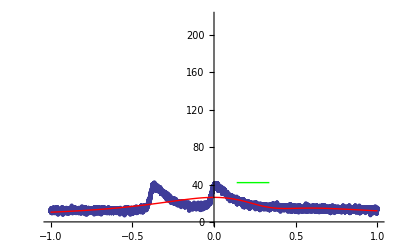

```mathematica
rawData = Import[NotebookDirectory[]<>"mod_abst_32cm.dat"];
messData = ToExpression[rawData];
Clear @ model;
model[x_] =k1/((1+(x-a1)^2/b1^2) b1 π)+k2/((1+(x-a2)^2/b2^2) b2 π) +c;
Peak = Max[messData];
nlm = NonlinearModelFit[messData, model[x], {{a1,-0.35},{ b1,0.1},{  k1, 18},{ a2,0.0},{  b2,0.1},{  k2,18},{  c,10}}, x];
nlmerrors = nlm["ParameterErrors"];
(*param=FindFit[messData, model[x], {{a1,0.1},{ b1,0.1},{  k1, 18},{ a2,0.3},{  b2,0.1},{  k2,18},{  c,10}}, x]*)
param=nlm["BestFitParameters"]
Distance = a2-a1 /. param
error = ((Part[nlmerrors, 1]*1.96)^2 + (Part[nlmerrors, 4]*1.96)^2)^0.5
Show[ListPlot[messData, PlotRange->{{-1, 1},{0,  220}}], Plot[model[x]  /. param, {x, -1, 1}, PlotRange->{{-1, 1},{0, 220}}, PlotStyle->Red], Graphics[{Green, Line[{{a1,Peak},{a2,Peak}} /. param]}]]
```

```mathematica
Peak
```